```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

Abaixo, temos os valores que y precisa assumir para que na terceira iteração do mapa logístico complexo, a parte imaginária seja nula. Percebemos que esses valores são funções de x e de μ. 
Refazendo o mesmo procedimento para x, encontramos 6 funções que são equivalentes às 6 últimas da célula anterior, com exceção da primeira que, apesar de ser trivial, não havia sido fornecida anteriormente.

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

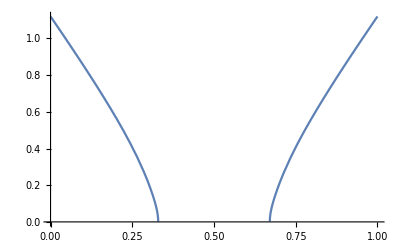

```mathematica
Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1}]
```

```mathematica
ys⟦4,1,2⟧[x]/.μ-> 3.8284
```

Part::partd: Part specification ys⟦4,1,2⟧ is longer than depth of object.

ys⟦4,1,2⟧[x]

```mathematica
xs = Solve[im==0,x]
```

{{x→1/2},{x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→1/2 (1-√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1-√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))}}

Então, no plano xy, encontramos os valores para os quais a componente imaginária será nula na terceira iteração.

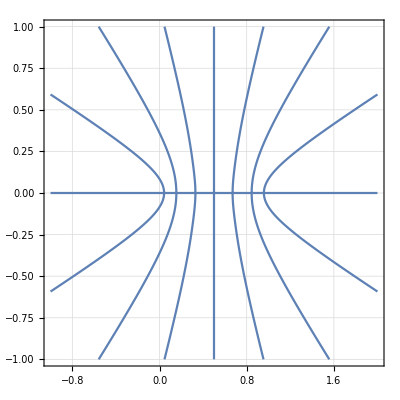

```mathematica
imμ =im/.μ-> 3.8284;
ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5]
```

Agora, nos deparamos com a seguinte pergunta:
Como se comportam os valores PRÓXIMOS das curvas de estabilidade que encontramos anteriormente? Podemos pensar em uma pequena variação ϵ com relação aos valores originais, e exigir que:

|Series[y_im]/y_s|< 1 , sendo:
y_im = componente imaginária da terceira iteração
     y_s = valor para o qual a componente imaginária da terceira iteração é 0

```mathematica
rlist={};
Do[AppendTo[rlist, FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,7}];
```

```mathematica
ϵlist = {};
Do[AppendTo[ϵlist, Reduce[Abs[rlist⟦i⟧]== 1,ϵ,Reals]],{i,1,6}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

```mathematica
partA = ϵlist⟦1,1,2,1,2⟧;
partB = ϵlist⟦2,1,2,1,2⟧;
```

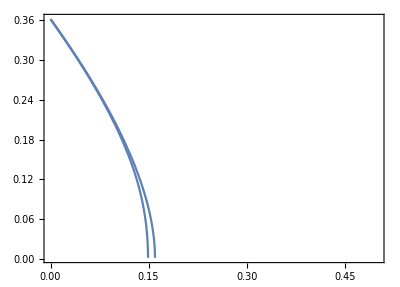

```mathematica
Show[ParametricPlot[{x0+partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0-partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5](*,ParametricPlot[{x0+partB, ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0-partB, ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5]*)]
```

```mathematica
ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}
```

(0.-0.36139 ⅈ) √(-1-7.6568 (-1+x0) x0)

```mathematica
ℛ=ParametricRegion[{{{x0-partA,ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},0≤x0≤0.5}},{x0}];
```

ParametricRegion::funs: {{{(1.84673×10^16)/(1.23542×10^20+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])+x0,(0.-0.36139 ⅈ) √(-1-7.6568 Plus[«2»] x0)},0≤x0≤0.5}} should be a non-empty list of real-valued functions of variables {x0}.

```mathematica
ParametricRegion[{{x0-partA<x0< x0+partA,ys⟦2,1,2⟧},{x0-partB<x0< x0+partB,ys⟦3,1,2⟧}},{{x0,0,0.5},{x0,0,0.5}}]
```

ParametricRegion::bcond: (1.84673×10^16)/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 Power[«2»]-3.2214×10^22 Power[«2»]+5.17229×10^22 Power[«2»]-4.27391×10^22 Power[«2»]+1.42464×10^22 Power[«2»])+x0<x0<-(1.84673×10^16)/(«9»+1.42464×10^22 Power[«2»])+x0&&(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ) should be a Boolean combination of equations, inequalities, and Element statements.

ParametricRegion[{{x0-partA<x0<x0+partA,ys⟦2,1,2⟧},{x0-partB<x0<x0+partB,ys⟦3,1,2⟧}},{{x0,0,0.5},{x0,0,0.5}}]

```mathematica
ℛ=ParametricRegion[{{t,s (1-t^2)},-1≤s≤1&&-1≤t≤1},{s,t}];
```

```mathematica
ParametricRegion[{{x0+partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{ x0-partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0+partB, ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}},{ x0-partB, ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}}},
```

```mathematica
ranges = {{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}};
```

```mathematica
dp = 0;
up  = 1;
pplots={};
Do[i= n-1;
Do[ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=0.9999ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= 1.00001ϵlist⟦i,j,1,1⟧;u = 0.999999ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=1.00001ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]],
{j,ranges⟦i⟧}],
{n,{2,3,4,5,6,7}}];
```

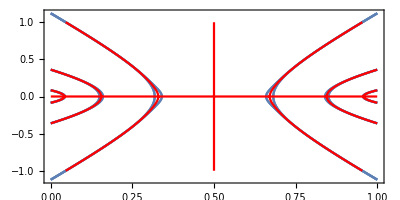

```mathematica
img = Show[pplots,ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic,ContourStyle->Red, MaxRecursion->5],PlotRange-> Automatic, AspectRatio-> 1/2]
```

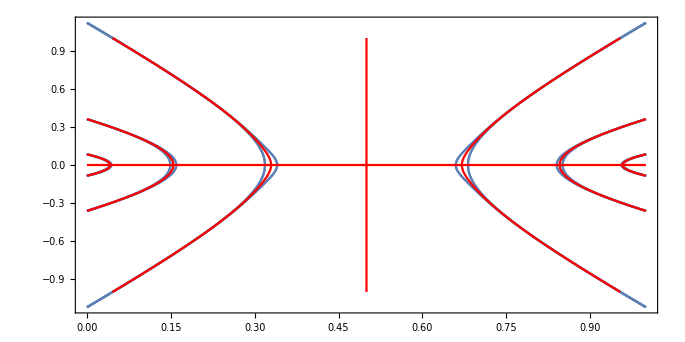
```mathematica
imgfinal2 = -Graphics-;
```

```mathematica
x
```

0.821507

```mathematica
bandax= FullSimplify[Normal[Series[im/y,{x,1/2,1}]/.μ-> 3.8284]/.x-> ϵ]
```

96429.8 (0.000729445+0.0346207 y^2+0.358191 y^4+1. y^6) (-0.5+1. ϵ)

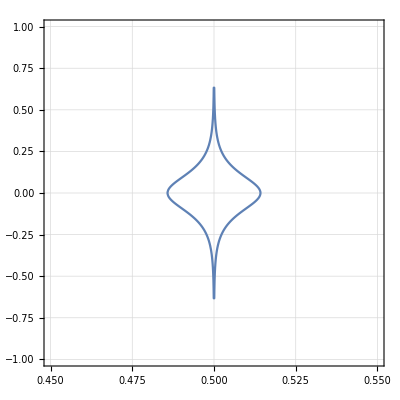

```mathematica
img2 = RegionPlot[Abs[bandax]< 1,{ϵ,0.45,0.55},{y,-1,1},GridLines->Automatic,MaxRecursion->5, PlotStyle->None]
```

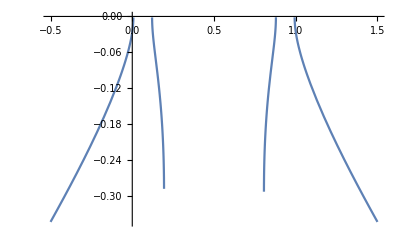

```mathematica
Plot[ys⟦4,1,2⟧/.μ-> 8.8284, {x,-0.5,1.5}]
```

Análise do destino dos pontos:

```mathematica
listadesejada = {{"0.5088","0.1164"},{"0.5029","0.01666"},{"0.4919","-0.07202"},{"0.5068","-0.07628"},{"0.4966","0.03349"},{"0.4966","0.1011"},{"0.5083","0.03095"},{"0.495","-0.1346"},{"0.5047","-0.1195"},{"0.495","-0.02382"}};
points = ToExpression[listadesejada];
```

```mathematica
μ=3.8284;
map1points = Table[ {Re[map[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}];
map2points = Table[ {Re[map2[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map2[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}];
map3points = Table[ {Re[map3[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map3[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}];
```

```mathematica
Do[
Do[xp = i⟦j,1⟧;
yp =  i⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points,{xp,yp}],{j,1,Length[i]}] ,{i,{map1points,map2points,map3points}}]
points = Partition[points,Length[listadesejada]];
```

```mathematica
map1points
```

{{0.859626,0.0989468},{0.84187,-0.0373724},{0.850074,0.000446284},{0.840725,0.0516338}}

```mathematica
map2points
```

{{0.499453,-0.272458},{0.515003,0.0978272},{0.487923,-0.00119624},{0.522853,-0.134706}}

```mathematica
map3points
```

{{1.24129,-0.00114147},{0.992877,-0.0112377},{0.956547,-0.000110622},{1.02457,0.0235712}}

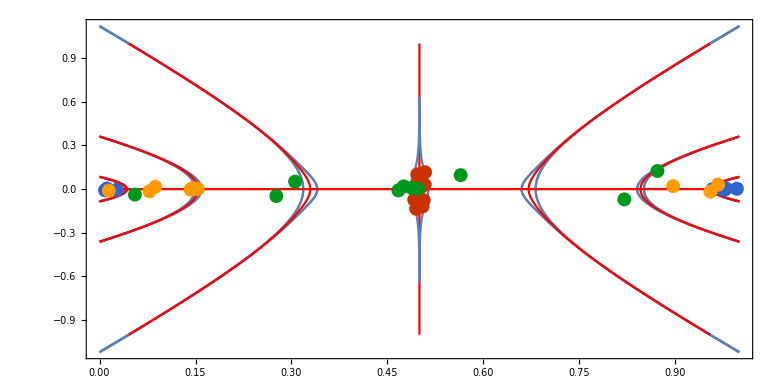

```mathematica
Show[img,img2,ListPlot[points, PlotTheme->"Web"]]
```

```mathematica
listameio={};
For[i=0,i≤ 100, i++;
px = RandomReal[{0.49,0.51}];
py = RandomReal[{-0.1,0.1}];
pt = {px,py};
AppendTo[listameio,pt]]
```

```mathematica
listameio3={};
μ=3.8284
For[i=0,i< Length[listameio],i++;
x0 = listameio⟦i,1⟧;
y0 = listameio⟦i,2⟧;
{x1,y1} = {Re[map[x0,y0,μ]],Im[map[x0,y0,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[listameio3,{x3,y3}]];
```

3.8284

{{0.507744,0.0000537829}}

```mathematica
listameio
```

{{0.499294,0.0580511},{0.501586,0.0936009},{0.502336,0.0369531},{0.498288,0.045459},{0.493015,-0.05492},{0.506461,-0.0984773},{0.507746,0.0750835},{0.503592,-0.0826088},{0.495257,0.0165913},{0.508821,-0.0789409},{0.497134,-0.0599999},{0.509836,-0.0994321},{0.490003,-0.0158248},{0.500482,0.097682},{0.50536,0.00647655},{0.503158,0.0626394},{0.505312,-0.0086253},{0.496335,-0.0781476},{0.507953,-0.0772362},{0.495145,0.0997729},{0.508489,0.0840005},{0.494662,0.0548838},{0.494045,0.050748},{0.495774,0.0914057},{0.503515,0.0578323},{0.49129,0.0619238},{0.49752,0.0121531},{0.506771,0.0433415},{0.509493,0.0331755},{0.499815,-0.0626016},{0.507475,0.0000318675},{0.492921,-0.0747239},{0.505848,0.00484328},{0.495186,0.0529816},{0.498002,-0.0120039},{0.495267,0.0368989},{0.494052,-0.00713869},{0.508036,0.0707552},{0.503782,0.0366211},{0.509145,-0.0873688},{0.504327,-0.0763533},{0.49018,0.0411996},{0.504876,-0.0408317},{0.491498,-0.0549066},{0.500495,-0.0509472},{0.501016,-0.0096665},{0.495051,0.0899038},{0.500316,0.0599559},{0.495106,0.0973437},{0.494832,0.0815968},{0.502941,-0.0352713},{0.494079,-0.0532589},{0.501752,0.0339451},{0.505653,0.0814652},{0.505994,0.0867863},{0.501923,0.0637197},{0.503489,-0.0584009},{0.496465,-0.0948666},{0.499408,0.063662},{0.498705,0.0864531},{0.501196,-0.063908},{0.506466,-0.0220074},{0.494659,-0.0516891},{0.493122,-0.03218},{0.503825,0.0508673},{0.490942,-0.0589938},{0.503608,-0.0914936},{0.492239,-0.0560228},{0.49255,0.0655901},{0.493656,0.0562756},{0.501906,-0.0965933},{0.496448,0.00129176},{0.508247,0.0508772},{0.502052,0.0881504},{0.50747,0.0612849},{0.4935,-0.0354312},{0.500007,0.0250976},{0.503805,0.0341966},{0.49952,-0.0218167},{0.504235,-0.0493428},{0.497349,0.0559369},{0.495682,-0.0918292},{0.491555,-0.0112882},{0.508422,0.0491541},{0.506848,-0.0105049},{0.491029,0.0361111},{0.498616,-0.0165873},{0.504963,-0.0336817},{0.498554,-0.0883123},{0.490694,0.0161802},{0.490533,-0.0453498},{0.49733,-0.0223824},{0.507181,-0.0369094},{0.498144,-0.0783685},{0.505728,0.0356849},{0.498455,-0.0843943},{0.495439,-0.0115051},{0.499327,0.0480309},{0.491849,0.0329124},{0.495533,0.0586152},{0.496053,-0.000193873}}

```mathematica
3.8284
```

3.8284

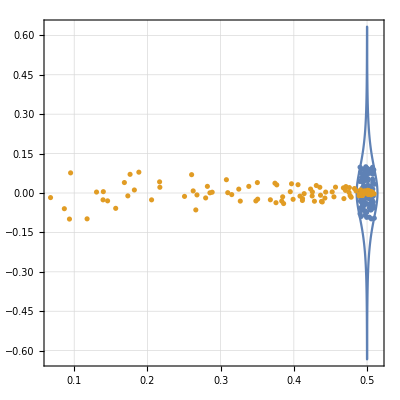

```mathematica
Show[img2,ListPlot[{listameio, listameio3}],PlotRange-> All]
```

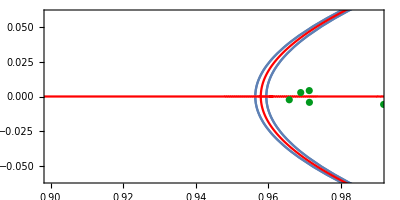

```mathematica
Show[img,img2,ListPlot[points, PlotTheme->"Web"],PlotRange-> {{0.9,0.99},{-0.06,0.06}}]
```

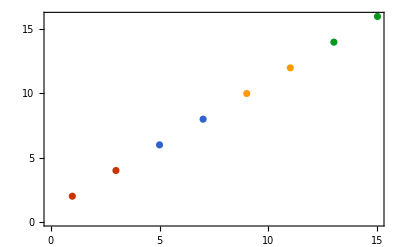

```mathematica
ListPlot[{{{1,2},{3,4}},{{5,6},{7,8}},{{9,10},{11,12}},{{13,14},{15,16}}},PlotTheme->"Web"]
```

Faremos agora o mesmíssimo tratamento, porém para map1 e map2:

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
```

```mathematica
im1 = y μ-2 x y μ;
im2 = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
```

```mathematica
ys1 =FullSimplify[ Solve[im1==0,y]]
xs1 = Solve[im1==0,x]
```

{{y→0}}

{{x→1/2}}

```mathematica
ys2=FullSimplify[ Solve[im2==0,y]]
xs2 = Solve[im2==0,x]
```

{{y→0},{y→-(√(-1+2 x) √(1-2 x μ+2 x^2 μ))/(√(-2 μ+4 x μ))},{y→(√(-1+2 x) √(1-2 x μ+2 x^2 μ))/(√(-2 μ+4 x μ))}}

{{x→1/2},{x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)}}

```mathematica
rlist2={};
Do[AppendTo[rlist2, FullSimplify[Normal[Series[im2/.x-> x0+ϵ,{ϵ,0,1}]]/ys2⟦i,1,2⟧/.{y-> ys2⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,3}];
```

```mathematica
ϵlist2 = {};
Do[AppendTo[ϵlist2, Reduce[Abs[rlist2⟦i⟧]== 1,ϵ,Reals]],{i,1,2}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

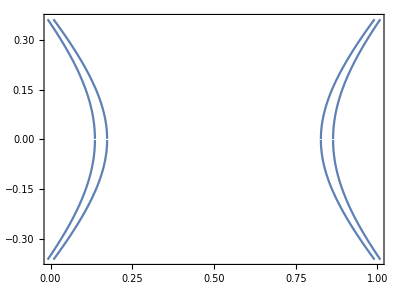

```mathematica
img3 = Show[ParametricPlot[{x0+ part1, ysn2⟦2,1,2⟧},{x0,0,0.5},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- part1, ysn2⟦2,1,2⟧},{x0,0,0.5},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ part1, ysn2⟦3,1,2⟧},{x0,0,0.5},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- part1, ysn2⟦3,1,2⟧},{x0,0,0.5},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ part1, ysn2⟦2,1,2⟧},{x0,0.5,1.0},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- part1, ysn2⟦2,1,2⟧},{x0,0.5,1.0},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ part1, ysn2⟦3,1,2⟧},{x0,0.5,1.0},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- part1, ysn2⟦3,1,2⟧},{x0,0.5,1.0},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]]
```

Tentativa de não utilizar o Series, mas sim o ys na sua forma mais pura.

```mathematica
fullrlist2={};
Do[AppendTo[fullrlist2, FullSimplify[(im2/.x-> x0+ϵ)/ys2⟦i,1,2⟧/.{y-> ys2⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,3}];
```

```mathematica
fullrlist2
```

{-112.223 ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ),-112.223 ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ)}

```mathematica
fullϵlist2 = {};
Do[AppendTo[fullϵlist2, Reduce[Abs[fullrlist2⟦i⟧]== 1,ϵ,Reals]],{i,1,2}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Resultado diferente do que obtivemos usando o series para o map2! Bem menos trivial.

```mathematica
fullϵlist2⟦1,3⟧
```

0.273789<x0<0.726211&&(ϵ==Root[8.87176×10^6+(9.95615×10^8-3.98246×10^9 x0+3.98246×10^9 x0^2) #1+(-2.98685×10^9+5.97369×10^9 x0) #1^2+1.99123×10^9 #1^3&,1]||ϵ==Root[-8.87176×10^6+(9.95615×10^8-3.98246×10^9 x0+3.98246×10^9 x0^2) #1+(-2.98685×10^9+5.97369×10^9 x0) #1^2+1.99123×10^9 #1^3&,1])

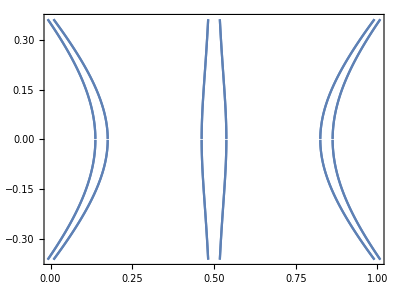

```mathematica
Show[ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦2,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0.27378920599089995,0.7262107940091},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0.27378920599089995,0.7262107940091},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦2,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],

ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦3,1,2⟧},{x0,0,0.27378920599089995},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0.27378920599089995,0.7262107940091},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0.27378920599089995,0.7262107940091},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,1], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+ Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,2], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],ParametricPlot[{x0+Root[8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+Root[-8.871758*^6+(9.95615399*^8-3.982461596*^9 x0+3.982461596*^9 x0^2) #1+(-2.986846197*^9+5.973692394*^9 x0) #1^2+1.991230798*^9 #1^3&,3], ysn2⟦3,1,2⟧},{x0,0.7262107940091,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]]
```

Interessante! Podemos tentar map3 sem Series:

```mathematica
fullrlist={};
Do[AppendTo[fullrlist, FullSimplify[(im/.x-> x0+ϵ)/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,7}];
```

```mathematica
fullϵlist = {};
Do[AppendTo[fullϵlist, Reduce[Abs[fullrlist⟦i⟧]== 1,ϵ,Reals]],{i,1,6}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

```mathematica
ranges = {{1,3,5,7,9,11,13},{1,3,5,7,9,11,13},{1,3,5,6,8,10,11,12,14,16,17,19,21},{1,3,5,6,8,10,11,12,14,16,17,19,21},{1,2,3,5,6,8,10,12,14,15,17,18,19},{1,2,3,5,6,8,10,12,14,15,17,18,19}};
roots = {{14,10,6,2,6,10,14},{14,10,6,2,6,10,14},{14,10,6,6,2,2,2,2,2,6,6,10,14},{14,10,6,6,2,2,2,2,2,6,6,10,14},{14,14,14,10,10,10,6,10,10,10,14,14,14},{14,14,14,10,10,10,6,10,10,10,14,14,14}};
```

```mathematica
dp = 0;
up  = 1;
pplots={};
Do[i= n-1;
Do[ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
Which[j ==ranges⟦i,1⟧,d=0;u=0.9999fullϵlist⟦i,j,1,2⟧;
Do[part = fullϵlist⟦i,j,2,k,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{k,roots⟦i,Flatten[Position[ranges⟦i⟧,j]]⟦1⟧⟧}],

j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= 1.00001fullϵlist⟦i,j,1,1⟧;u = 0.999999fullϵlist⟦i,j,1,5⟧;
Do[part = fullϵlist⟦i,j,2,k,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{k,roots⟦i,Flatten[Position[ranges⟦i⟧,j]]⟦1⟧⟧}],

j == ranges⟦i,-1⟧, d=1.00001fullϵlist⟦i,j,1,2⟧; u=1;
Do[part = fullϵlist⟦i,j,2,k,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{k,roots⟦i,Flatten[Position[ranges⟦i⟧,j]]⟦1⟧⟧}]],
{j,ranges⟦i⟧}],
{n,{2,3,4,5,6,7}}];
```

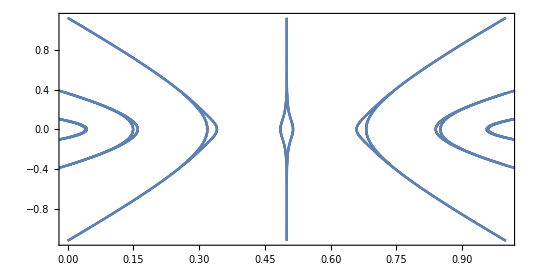

```mathematica
imgfinal = Show[pplots,AspectRatio-> 1/2]
```

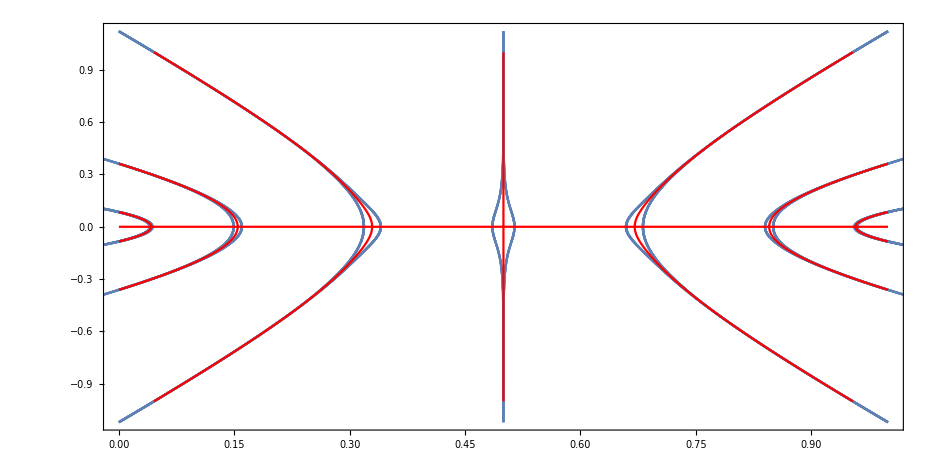

```mathematica
Show[imgfinal,imgfinal2]
```

Bandas de Atração por Interpolação

Quais são os valores de corte??

```mathematica
x0s = xs/.{μ-> 3.8284, y-> 0}
```

{{x→1/2},{x→0.154461},{x→0.845539},{x→0.329294},{x→0.670706},{x→0.0421202},{x→0.95788}}

Segunda banda:

```mathematica
ϵlist⟦1,1,2,1,2⟧
```

-(1.84673×10^16)/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)

```mathematica
- (ϵlist⟦1,1,2,1,2⟧/.x0-> x0s⟦2,1,2⟧ ) + x0s⟦2,1,2⟧
```

0.159792

```mathematica
(ϵlist⟦1,1,2,1,2⟧/.x0-> x0s⟦2,1,2⟧ ) + x0s⟦2,1,2⟧
```

0.14913

Primeira banda:

```mathematica
- (ϵlist⟦3,1,2,1,2⟧/.x0->x0s⟦6,1,2⟧) + x0s⟦6,1,2⟧
```

0.0436382

```mathematica
(ϵlist⟦3,1,2,1,2⟧/.x0-> x0s⟦6,1,2⟧ ) + x0s⟦6,1,2⟧
```

0.0406023

Terceira banda:

```mathematica
- (ϵlist⟦5,1,2,1,2⟧/.x0-> x0s⟦4,1,2⟧ ) + x0s⟦4,1,2⟧
```

0.296005

```mathematica
(ϵlist⟦5,1,2,1,2⟧/.x0->x0s⟦4,1,2⟧) + x0s⟦4,1,2⟧
```

0.362584

```mathematica
{{"0.3198","0.004326"},{"0.148","0.006776"}}
```

```mathematica
{{"0.3186","0.005893"}}
```

```mathematica
maxvalues = {0.043638217953774955,0.1597920544491029,0.3388};
minvalues = {0.04060225362270445,0.14913012884644786,0.3186};
```

```mathematica
(ϵlist⟦6,1,2,1,2⟧/.x0-> 0 )
```

-2.5416×10^-6

```mathematica
- (ϵlist⟦5,1,2,2,2⟧/.x0-> 0 )
```

-2.5416×10^-6

```mathematica
partA = ϵlist⟦1,1,2,1,2⟧;
listamax = Table[{x0-partA,  ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.0000001,maxvalues⟦2⟧,0.00001}];
AppendTo[listamax,{maxvalues⟦2⟧,0}];
f2max = Interpolation[listamax, InterpolationOrder->2, Method->"Hermite"];
f2min = Interpolation[Table[{x0+partA,  ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.000000000001,minvalues⟦2⟧,0.00001}]];
```

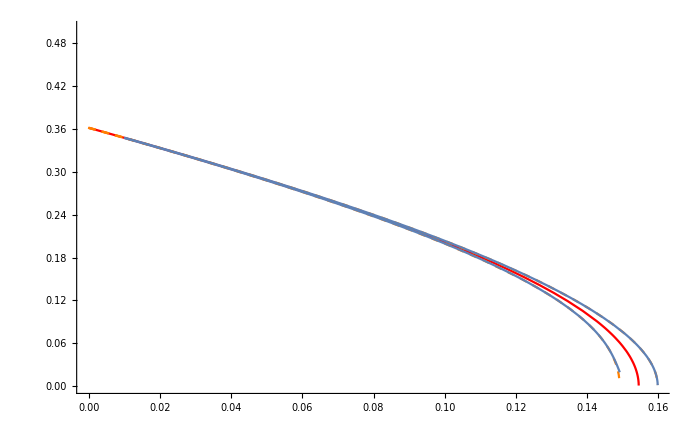

```mathematica
Show[Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,0.2}, PlotRange-> {All,{0,0.5}}, PlotStyle->{Red}],ParametricPlot[{x0+partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5,PlotStyle->{Orange,Dashed}],ParametricPlot[{x0-partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5,PlotStyle->{Orange,Dashed}],
Plot[f2max[x0],{x0,0.01,maxvalues⟦2⟧}],Plot[f2min[x0],{x0,0.01,minvalues⟦2⟧}]]
```

```mathematica
{{0.15925732801634485,0.004726695783529911}}
```

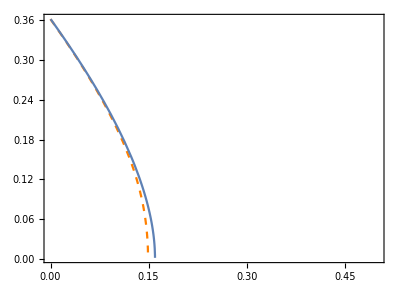

```mathematica
Show[ParametricPlot[{x0+partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5,PlotStyle->{Orange,Dashed}],ParametricPlot[{x0-partA, ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}},{x0,0,0.5},PlotRange->{{0,0.5},All},Frame->True,MaxRecursion->5]]
```

```mathematica
partA = ϵlist⟦3,1,2,1,2⟧;
listamax = Table[{x0-partA,  ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.000000000001,maxvalues⟦1⟧,0.00001}];
AppendTo[listamax,{maxvalues⟦1⟧,0}];
f1max = Interpolation[listamax];
f1min = Interpolation[Table[{x0+partA,  ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.0000000001,minvalues⟦1⟧,0.00001}]];
```

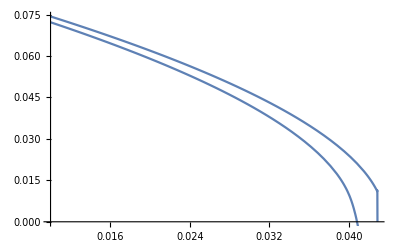

```mathematica
Show[Plot[f1max[x0],{x0,0.01,0.04288859263679885}],Plot[f1min[x0],{x0,0.01,0.04135187893968055}]]
```

```mathematica
ranges = {{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}};
```

```mathematica
dp = 0;
up  = 1;
pplotsmin={};
pplotsmax={};
Do[i= n-1;
Do[ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=0.999999999999ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= 1.00000000001ϵlist⟦i,j,1,1⟧;u = 0.999999999999ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=1.00000000001ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplotsmin,Table[{x0+part1, ysn},{x0,d,u,0.0001}]];
AppendTo[pplotsmax,Table[{x0-part1, ysn},{x0,d,u,0.0001}]],
{j,ranges⟦i⟧}],
{n,{7}}];
```

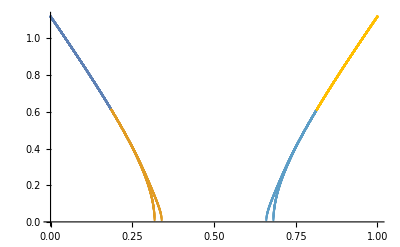

```mathematica
Show[ListPlot[pplotsmax],ListPlot[pplotsmin]]
```

```mathematica
pplots2min = Flatten[pplotsmin,1];
idelmin={};
For[i=0,i<Length[pplots2min],i++;
If[(Im[pplots2min⟦i,2⟧]≠ 0),AppendTo[idelmin,{i}],None];
If[pplots2min⟦i,1⟧> 0.5, AppendTo[idelmin,{i}],None]]

pplots2max = Flatten[pplotsmax,1];
idelmax={};
For[i=0,i<Length[pplots2max],i++;
If[(Im[pplots2max⟦i,2⟧]≠ 0),AppendTo[idelmax,{i}],None];
If[pplots2max⟦i,1⟧> 0.5, AppendTo[idelmax,{i}],None]]

listamax = Delete[pplots2max, idelmax];
AppendTo[listamax,{maxvalues⟦3⟧,0}];

f3max= Interpolation[listamax,Method->"Spline",InterpolationOrder->2];
f3min= Interpolation[Delete[pplots2min, idelmin],Method->"Hermite",InterpolationOrder->2];
```

Greater::nord: Invalid comparison with 0.325868-2.20404×10^-6 ⅈ attempted.

Greater::nord: Invalid comparison with 0.412929+2.20404×10^-6 ⅈ attempted.

```mathematica
pplots2max
```

{{0,132.412},{0.000102545,132.412},{0.000202548,132.412},{0.000302551,132.412},9998,{0.999695,132.412},{0.999795,132.412},{0.999895,132.412},{0.999995,132.412}}
 |  |  |  |

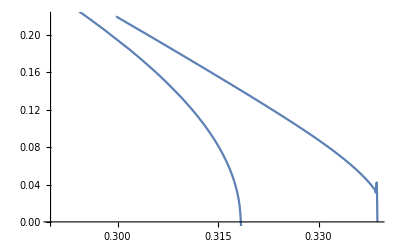

```mathematica
Show[Plot[f3max[x0],{x0,0.29,maxvalues⟦3⟧},PlotRange->{0,0.22}],Plot[f3min[x0],{x0,0.36,minvalues⟦3⟧}]]
```

```mathematica
band1pts = {};
up =maxvalues⟦1⟧;
For[i=0,i<3000,i++;
px= RandomReal[{0,up}];
If[px<minvalues⟦1⟧,pmax = Re[f1max[px]];pmin = Re[f1min[px]], 
pmax=Re[f1max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band1pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.039528} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0399068} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0399447} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
band2pts = {};
up =maxvalues⟦2⟧;
For[i=0,i<3000,i++;
px= RandomReal[{0,up}];
If[px<minvalues⟦2⟧,pmax = Re[f2max[px]];pmin = Re[f2min[px]], 
pmax=Re[f2max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band2pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.14556} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.146481} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.147317} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
band3pts = {};
up =maxvalues⟦3⟧;
For[i=0,i<7000,i++;
px= RandomReal[{0,up}];
If[px<minvalues⟦3⟧,pmax = Re[f3max[px]];pmin = Re[f3min[px]], 
pmax=Re[f3max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band3pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.318399} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.318415} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.318553} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

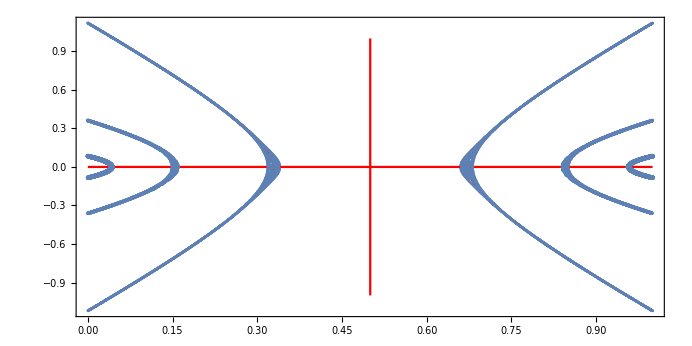

```mathematica
Show[img,ListPlot[band2pts],ListPlot[band1pts], ListPlot[band3pts]]
```

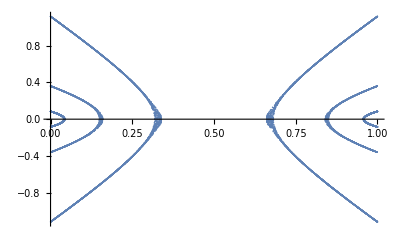

```mathematica
totalbands = Flatten[{band1pts,band2pts,band3pts},1];
ListPlot[totalbands]
```

```mathematica
μ=3.8284;
  stats={};
For[i=0,i< Length[totalbands],i++;
x = totalbands⟦i,1⟧;
y = totalbands⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[stats,{x,y}]]
```

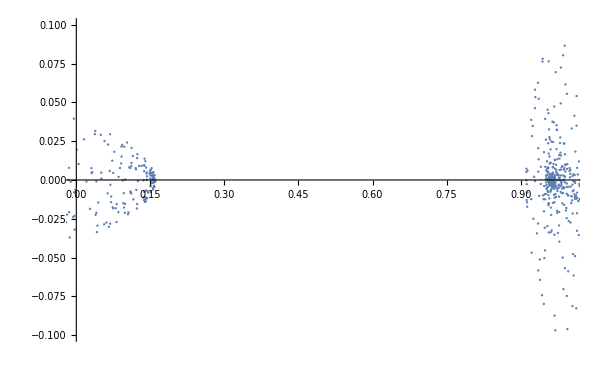

```mathematica
ListPlot[stats,PlotRange->{{0,1},{-0.1,0.1}}]
```

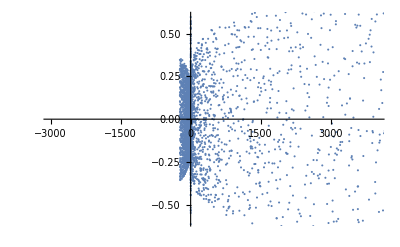

```mathematica
ListPlot[stats,PlotRange->{{-3000,4000},{-0.6,0.6}}]
```

Faz sentido encontrarmos esse valores para x?? Olhar para o mapa logístico.